# EDO Logística dy/dt= ry(1 - y/K)

r es la tasa de crecimiento y K es la capacidad de carga. Consideramos r, K > 0

Editor:      Roberto Méndez
Edición.   29 Aug 24   v1

2

1

(1-y/2) y

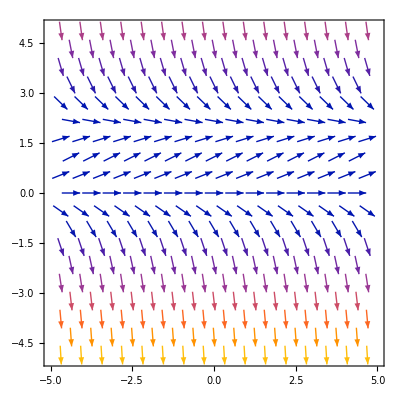

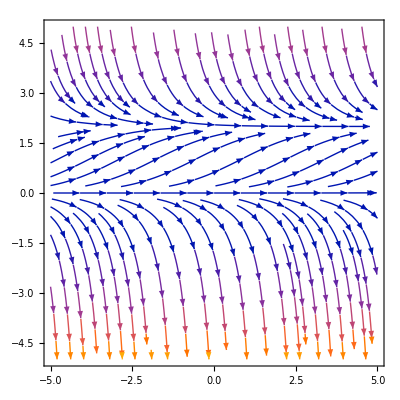

```mathematica
K = 2
r = 1
f[x_,y_]= r*y*(1 - y/K)
VectorPlot[{1,f[x,y]},{x,-5,5},{y,-5,5}]
StreamPlot[{1,f[x,y]},{x,-5,5},{y,-5,5}]
```